## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/InOutTransitions

RandomPointsPlot

RandomPointsMatrix

```mathematica
"/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/BRInE"
```

/Users/sanchez.hmsc/Documents/GitHub/MGDrivE/BRInE

```mathematica
"RandomPointsPlot"
```

RandomPointsPlot

```mathematica
"RandomPointsMatrix"
```

RandomPointsMatrix

## Routine

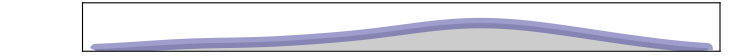
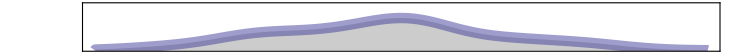
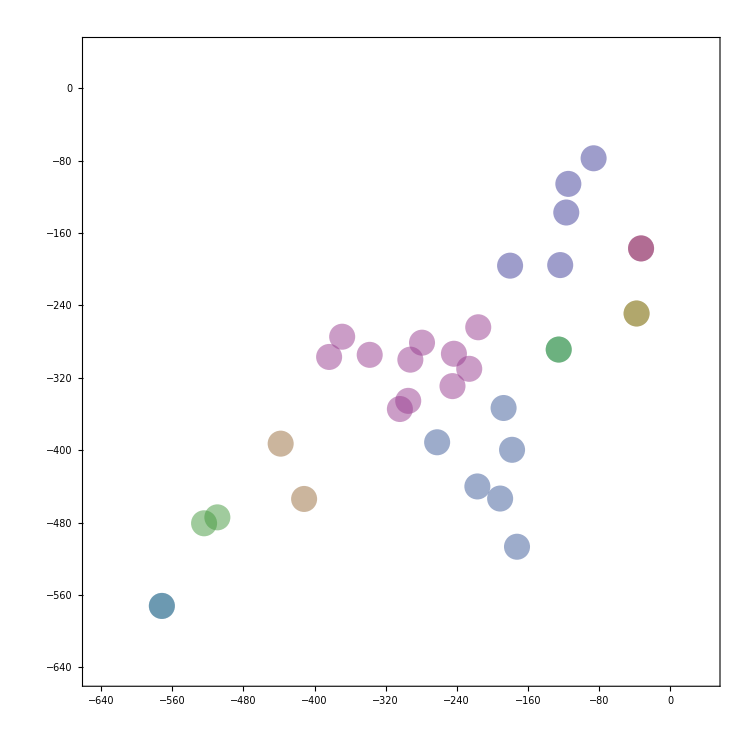
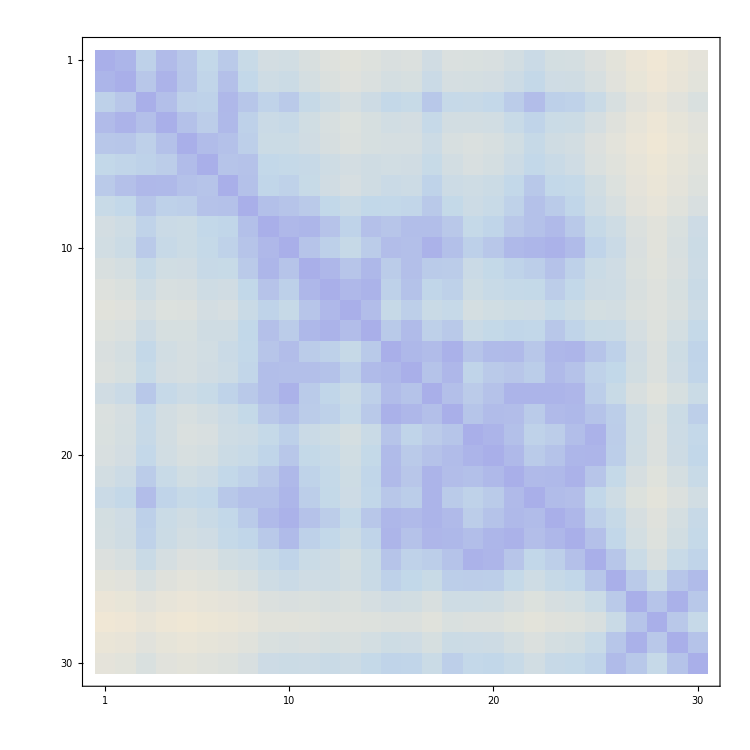
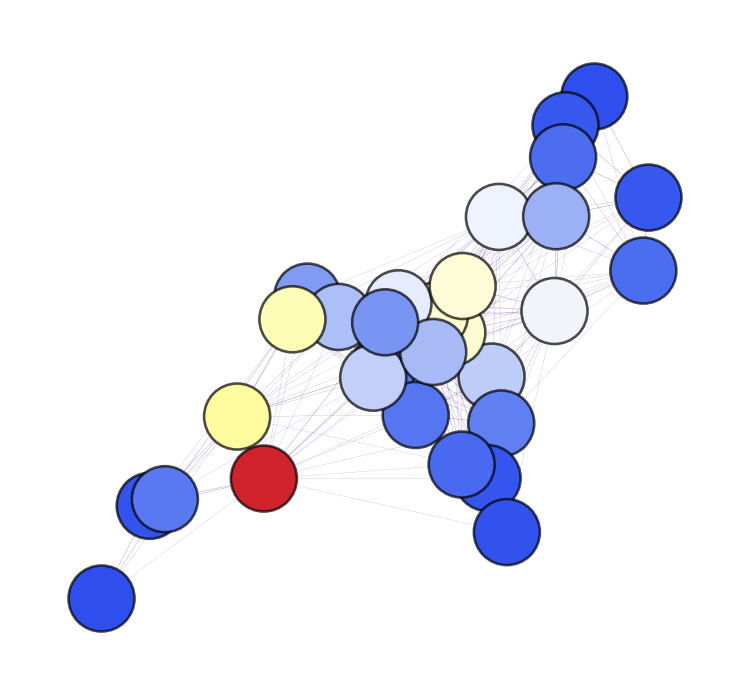
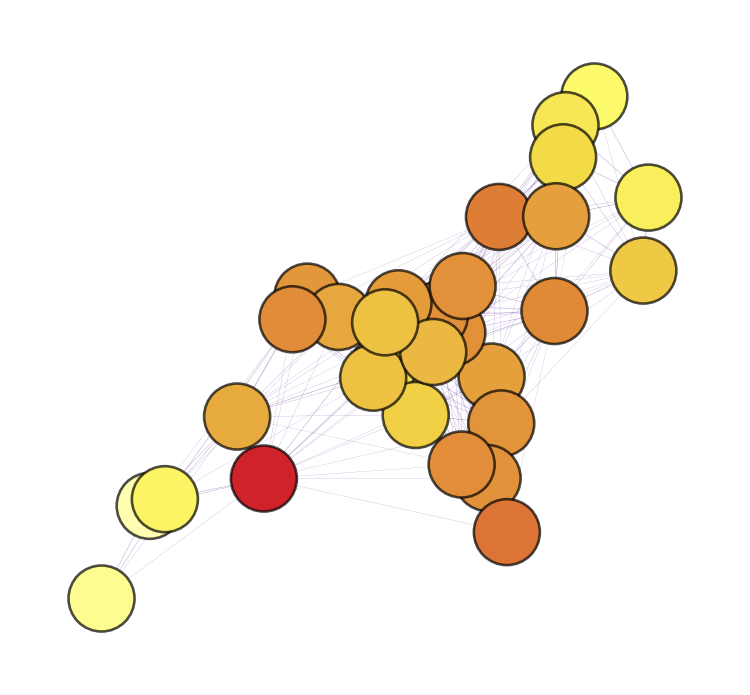
| -Graphics- | 
-Graphics- | -Graphics- |  | -Graphics-
-Graphics- | -Graphics-

randomNetworkWithCentrality.png

```mathematica
citiesDummy = Accumulate[RandomReal[{-100, 100}, {30, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
distances = CalculateEuclideanDistances[citiesDummy];
migration = CalculateMigrationProbabilities[distances, 1000];
{min, max} = {Flatten[citiesDummy] // Min, Flatten[citiesDummy] // Max};
{imageSize, imagePadding, plotRange} = {750, 50, {{min - 75, max + 75}, {0, .005}}};
sampledCoordinates = citiesDummy;
clusteredCoordinates = FindClusters[sampledCoordinates, Method -> "NeighborhoodContraction"];
eucledianDistances = CalculateEuclideanDistances[sampledCoordinates];
(**)
histograms = SmoothHistogramPlot[#, {imageSize, imagePadding}, plotRange] & /@ Transpose[sampledCoordinates];
scatter = ListPlotScatter[clusteredCoordinates, {imageSize, imagePadding}, plotRange];
grid = Grid[{
    {"", Rotate[histograms[[1]] // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {0, 0}}] &, 0 Degree], ""},
    {Rotate[histograms[[2]] // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {0, 0}}] &, 90 Degree], scatter // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {imagePadding, imagePadding}}] &, ""}
    }];
graph = GraphTransitionsFrequenciesWithMax[
   {
    Chop[Quiet[1/eucledianDistances] // ReplacePart[#, {i_, i_} -> 0] &, .004],
    ToString /@ Range[Length[citiesDummy]]
    }, .0001
   ];
graph2 = GraphTransitionsFrequenciesWithMax[
   {
    Chop[Quiet[1/eucledianDistances] // LowerTriangularize // ReplacePart[#, {i_, i_} -> 0] &, .004],
    ToString /@ Range[Length[citiesDummy]]
    }, .0001,
   VertexCoordinates -> ToExpression[citiesDummy],
   LineThickness -> .0000025,
   ImageSize -> 500,
   VertexStyle -> Directive[Lighter[Pink, 0.75], EdgeForm[Directive[Thickness[.0025], Black]]],
   VertexLabelStyle -> Directive[2.5, Opacity[0]],
   VariableStyle -> "Both",
   VertexSize -> 5
   ];
cc = BetweennessCentrality[graph];
cc1g = HighlightGraph[graph2, Table[Style[VertexList[graph][[i]], ColorData["TemperatureMap"][cc[[i]]/Max[cc]]], {i, VertexCount[graph]}], ImageSize -> 750];
(*Export["centralityBetweenNetwork.png",%,ImageSize->2500,ImageResolution->500];*)
cc = ClosenessCentrality[graph];
cc2g = HighlightGraph[graph2, Table[Style[VertexList[graph][[i]], ColorData["TemperatureMap"][cc[[i]]/Max[cc]]], {i, VertexCount[graph]}], ImageSize -> 750];
(*Export["centralityClosenessNetwork.png",%,ImageSize->2500,ImageResolution->500];*)
Grid[{{cc1g, cc2g}}];
grid = Grid[{
   {grid, MatrixPlot[eucledianDistances, ColorFunction -> "LakeColors", ImageSize -> imageSize]},
   {cc1g, cc2g}
   }]
Export["randomNetworkWithCentrality.png", grid, ImageSize -> 2500, ImageResolution -> 250]
```

## Generate Bipartite Network

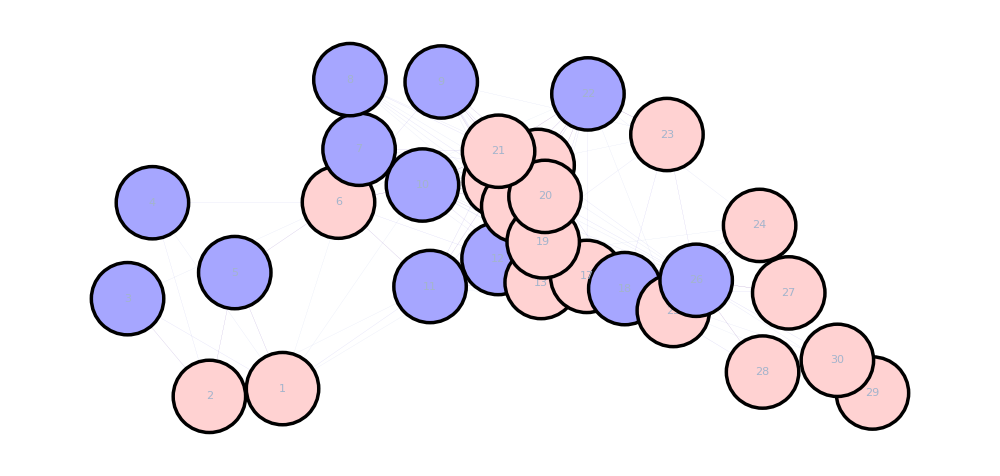

bipartiteNetwork.png

```mathematica
inMatrix = Chop[Quiet[1/eucledianDistances] // ReplacePart[#, {i_, i_} -> 0] &, .004];
id = RandomChoice[{"A", "B"}, Length[inMatrix]];
mask = Table[
   If[
    id[[i]] == "A",
    ReplaceAll[id, {"A" -> 0, "B" -> 1}],
    ReplaceAll[id, {"A" -> 1, "B" -> 0}]
    ]
   , {i, 1, Length[inMatrix]}];
Prepend[Prepend[mask // Transpose, id] // Transpose, Prepend[id, ""]] // MatrixForm;
style = If[# == "A", Directive[Lighter[Blue, 0.65], EdgeForm[Directive[Thickness[.0025], Black]]], Directive[Lighter[Pink, 0.65], EdgeForm[Directive[Thickness[.0025], Black]]]] & /@ id;
ids = ToString /@ Range[style // Length];
stylesList = (#[[2]] -> #[[1]]) & /@ ({style, ids} // Transpose);

graph = GraphTransitionsFrequenciesWithMax[
  {
   Chop[inMatrix*mask],
   ToString /@ Range[Length[inMatrix]]
   }, .01
  ];
graph2 = GraphTransitionsFrequenciesWithMax[
  {
   Chop[inMatrix*mask]//LowerTriangularize//Chop,
   ToString /@ Range[Length[inMatrix]]
   }, .01,
  VertexStyle -> stylesList,
  VertexCoordinates -> sampledCoordinates,
  VertexSize -> 2.5,
  ImageSize -> 1000,
  LineThickness -> .0001
  ]
Export["bipartiteNetwork.png", grid, ImageSize -> 2500, ImageResolution -> 250]
```

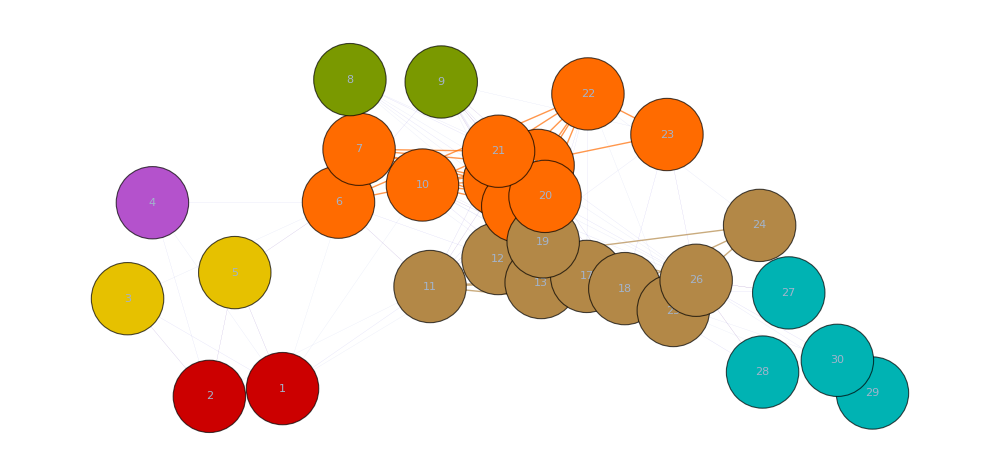

```mathematica
clusters=FindClusters[cities[[All,2]],Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusters[[i]]],{i,1,clusters//Length}];
highlighted=HighlightGraph[graph2,Map[Subgraph[graph2,#]&, clustersStrings]]
```

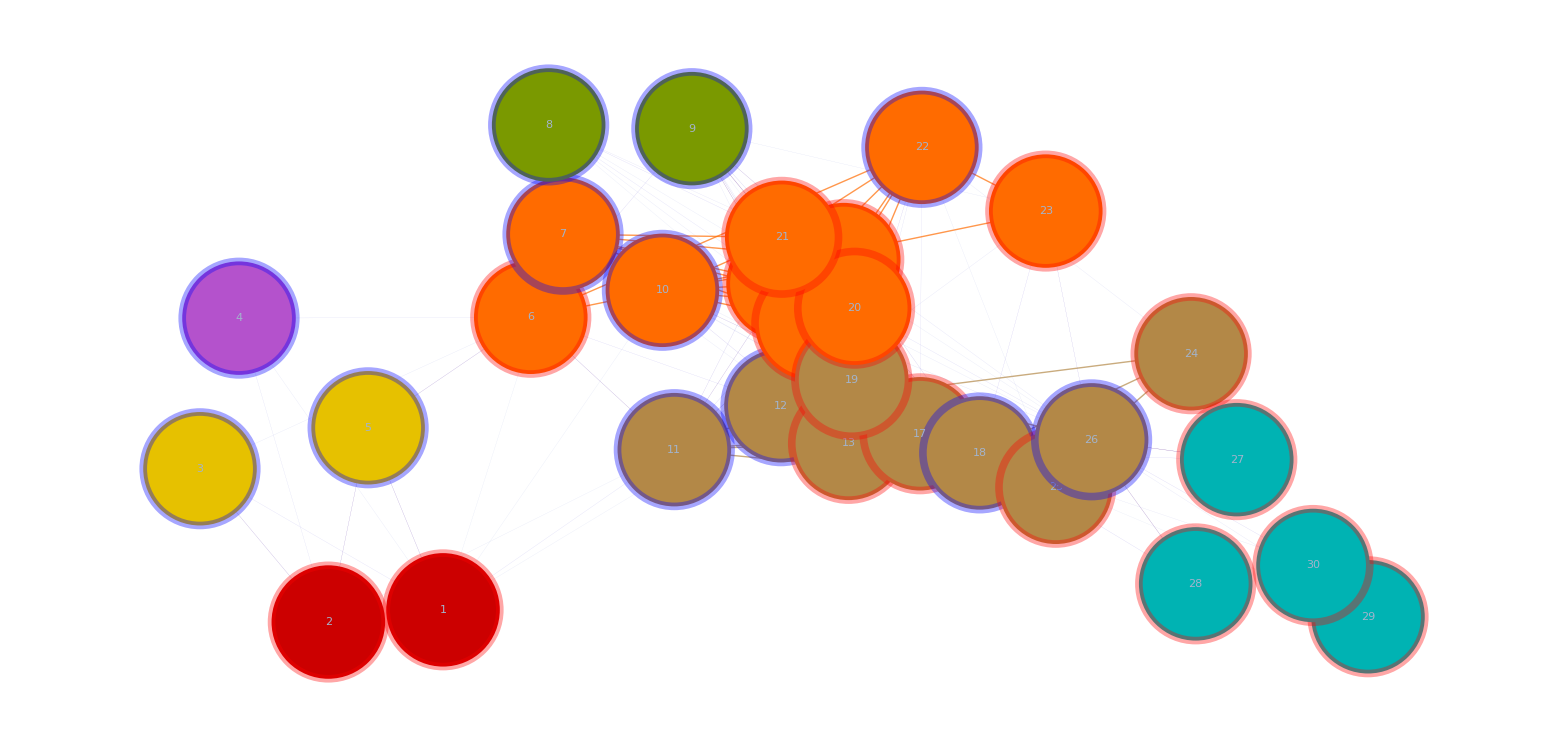

```mathematica
style2 = If[# == "A",EdgeForm[Directive[Thickness[.0035], Opacity[.35],Lighter[Blue, 0]]],  EdgeForm[Directive[Thickness[.0035],Opacity[.35], Lighter[Red,0]]]] & /@ id;
stylesList2 = Style[#[[2]] , #[[1]]] & /@ ({style2, ids} // Transpose);
HighlightGraph[highlighted,stylesList2,ImageSize->2000]
```

## Generate N-partite Network

```mathematica
inMatrix = Chop[Quiet[1/eucledianDistances] // ReplacePart[#, {i_, i_} -> 0] &, .004];
id = RandomChoice[{"A", "B","C","D"}, Length[inMatrix]];
mask = Table[
 Switch[id[[i]] ,
"A",ReplaceAll[id, {"A" -> 0, "B" -> 1,"C" -> 0,"D" -> 0}],
"B",   ReplaceAll[id,{"A" -> 0, "B" -> 0,"C" -> 1,"D" -> 0}],
"C",   ReplaceAll[id,{"A" -> 0, "B" -> 0,"C" -> 0,"D" ->1}],
"D",   ReplaceAll[id,{"A" -> 1, "B" -> 0,"C" -> 0,"D" -> 0}]
    ]
   , {i, 1, Length[inMatrix]}];
Prepend[Prepend[mask // Transpose, id] // Transpose, Prepend[id, ""]] // MatrixForm;
style = Switch[# ,
"A", Directive[Lighter[Blue, 0.65],EdgeForm[Directive[Opacity[1],Thickness[.005]]]],
"B", Directive[Lighter[Pink, 0.65],EdgeForm[Directive[Opacity[1],Thickness[.005]]]],
"C", Directive[Lighter[Purple, 0.65],EdgeForm[Directive[Opacity[1],Thickness[.005]]]],
"D", Directive[Lighter[Green, 0.65],EdgeForm[Directive[Opacity[1],Thickness[.005]]]]
] & /@ id;
ids = ToString /@ Range[style // Length];
stylesList = (#[[2]] -> #[[1]]) & /@ ({style, ids} // Transpose);

graph = GraphTransitionsFrequenciesWithMax[
  {
   Chop[inMatrix*mask],
   ToString /@ Range[Length[inMatrix]]
   }, .01
  ];
graph2 = GraphTransitionsFrequenciesWithMax[
  {
   Chop[inMatrix*mask]//Chop,
   ToString /@ Range[Length[inMatrix]]
   }, .01,
  VertexStyle -> stylesList,
  VertexCoordinates -> sampledCoordinates,
  VertexSize ->1.5,
VertexLabelStyle->20,
  ImageSize -> 1000,
  LineThickness -> .001
  ];
distance=Chop[ReplaceAll[#,ComplexInfinity->0]&/@Quiet[1/eucledianDistances]]//LowerTriangularize//Chop;
edgeshape2[e_,___]:={Arrowheads[{{.0000001,1}}],Arrow[e]}
graph3 = GraphTransitionsFrequenciesWithMax[
  {
Table[If[#>Mean[Flatten[distance]],#,0]&/@distance[[i]],{i,1,Length[distance]}],
ToString /@ Range[Length[inMatrix]]
   }, .01,
  VertexStyle -> stylesList,
  VertexCoordinates -> sampledCoordinates,
  VertexSize -> 1.5,
VertexLabelStyle->20,
  ImageSize -> 1000,
  LineThickness -> .001,
EdgeShapeFunction->edgeshape2
  ];
(*Export["bipartiteNetwork.png", grid, ImageSize -> 2500, ImageResolution -> 250]*)
```

```mathematica
clusters=FindClusters[cities[[All,2]],Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusters[[i]]],{i,1,clusters//Length}];
highlighted=HighlightGraph[graph2,Map[Subgraph[graph2,#]&, clustersStrings]];
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clusters])]]//Flatten//RandomSample;
```

```mathematica
frequencies=GetCommunitiesInOutTransitionsFrequencies[{inMatrix*mask,   ToString /@ Range[Length[inMatrix]]},clustersStrings]//Quiet;
(*ratios=GetCommunitiesInOutTransitionsRatios[{inMatrix*mask,   ToString /@ Range[Length[inMatrix]]},clustersStrings]//Quiet//ReplaceAll[#,Indeterminate->∞]&;*)
communities=Map[ToExpression,clustersStrings,Infinity]
(**)
outCommunity=Table[
comm=communities[[i]];
transitions=Chop[inMatrix*mask];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}]
inCommunity=Table[
comm=communities[[i]];
transitions=Chop[inMatrix*mask]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}]
ratios=Quiet[inCommunity/outCommunity]//ReplaceAll[#,ComplexInfinity->10]&
sinkSourceGrid=Grid[{(*colors[[1;;Length[ratios]]],*)Style[PaddedForm[#,3],15,Bold]&/@ratios,Style[#,12.5,Bold]&/@(If[#<1,"Source","Sink"]&/@ratios)},Frame->True,Background->{Lighter[#,0.1]&/@colors[[1;;Length[ratios]]],None},ItemSize->5];
flattenedRatios=Table[ConstantArray[ratios[[i]],clusters[[i]]//Length],{i,1,clusters//Length}]//Flatten
```

{{1,2,3,4,7},{5},{6},{8},{9,11,12,13,14,16},{10,15,17,18,19,20,21,22,23,24,25},{26,30},{27,29},{28}}

{0.0700279,0.0191925,0.0196878,0.0672756,0.175939,0.200153,0.0455425,0.00864378,0.0130827}

{0.095928,0.0199976,0.0259851,0.018206,0.141829,0.237166,0.0499794,0.0254288,0.00502614}

{1.36985,1.04195,1.31986,0.270618,0.806124,1.18492,1.09742,2.94186,0.384183}

{1.36985,1.36985,1.36985,1.36985,1.36985,1.04195,1.31986,0.270618,0.806124,0.806124,0.806124,0.806124,0.806124,0.806124,1.18492,1.18492,1.18492,1.18492,1.18492,1.18492,1.18492,1.18492,1.18492,1.18492,1.18492,1.09742,1.09742,2.94186,2.94186,0.384183}

```mathematica
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
geoClusters2=HighlightGraph[graph3, Style[#[[2]] ,Directive[EdgeForm[Directive[Opacity[1],Black,Thickness[.005]]],#[[1]]]] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)];
```

```mathematica
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
geoClusters3=HighlightGraph[graph2, Style[#[[2]] ,Directive[EdgeForm[Directive[Opacity[1],Thickness[.005(*Abs[1-#[[3]]]*.0075*)],If[#[[3]]>1,Darker[Blue,.25],Darker[Red,.25]]]],#[[1]]]] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)];
```

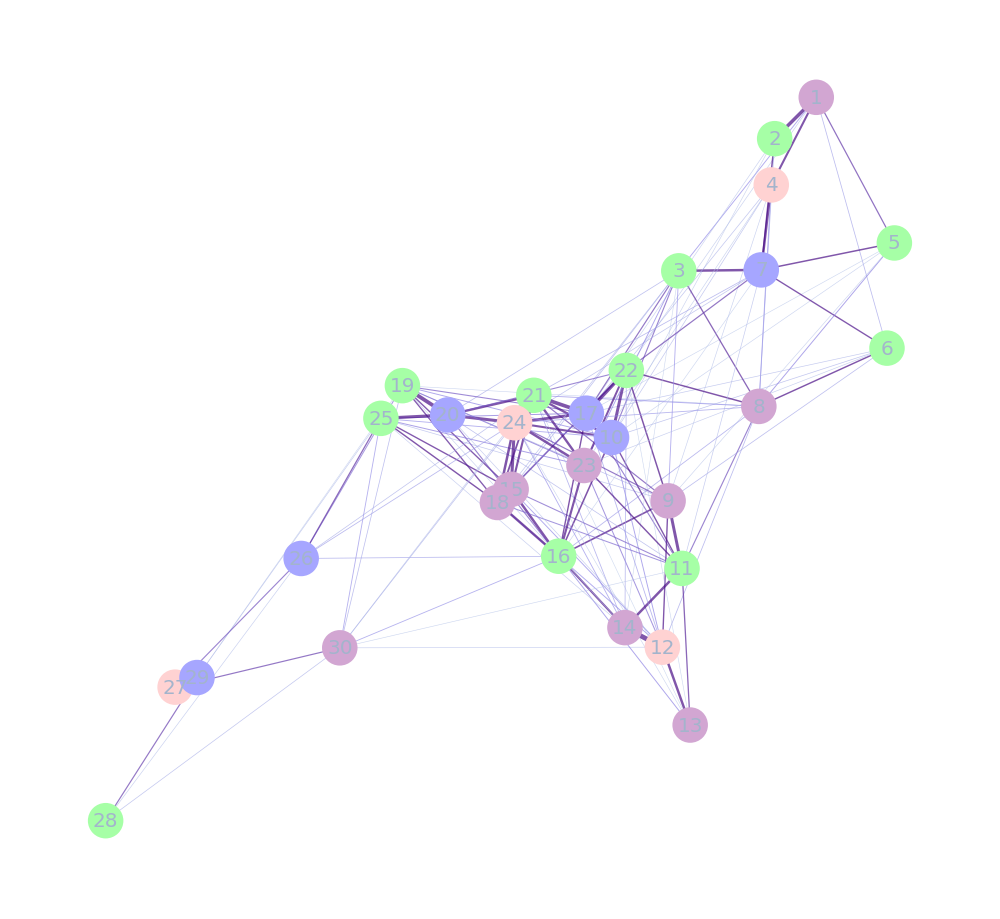
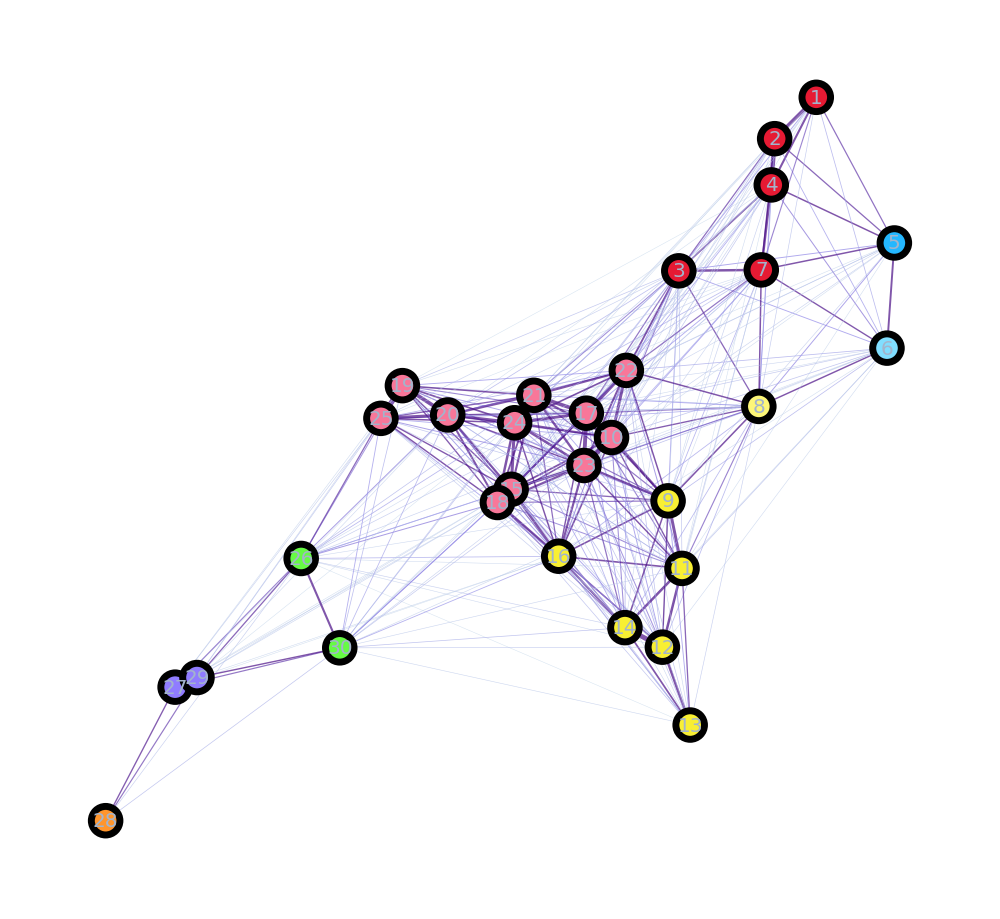
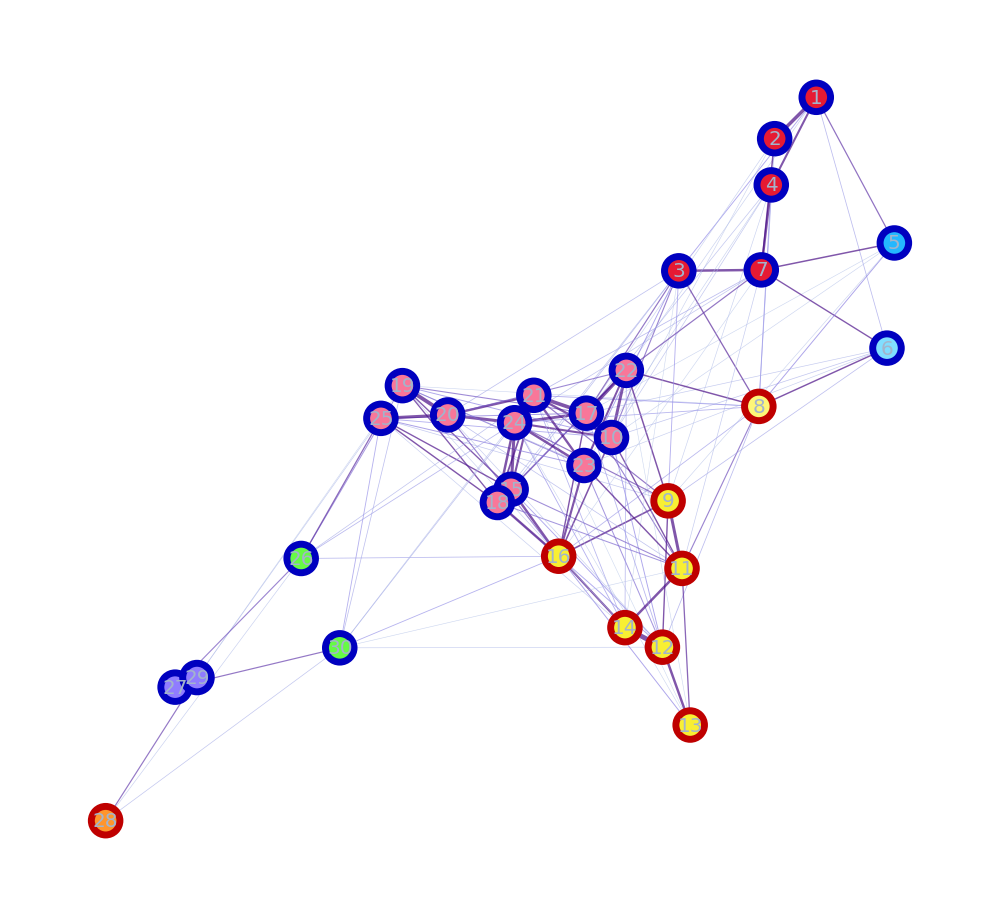
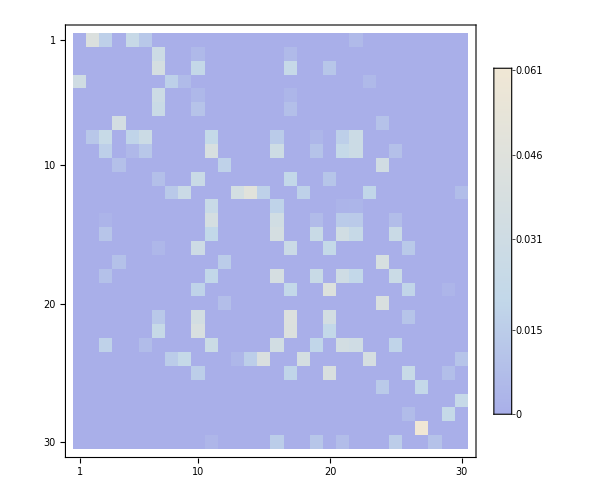
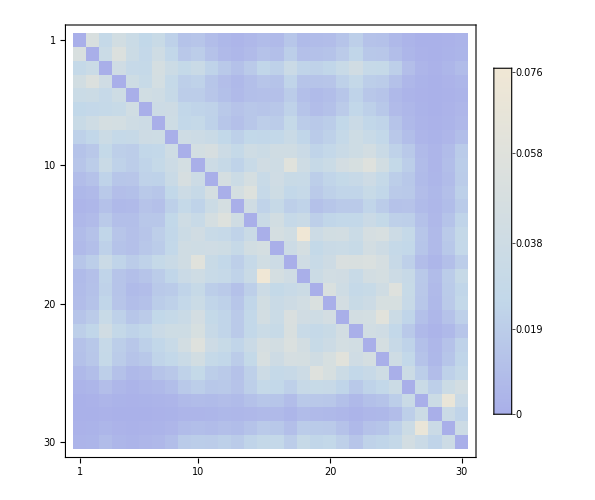
Point Type (M,F,L,S?) | Geo-Cluster | Source/Sink Analysis
-Graphics- | -Graphics- | -Graphics-
 |  | 
-Graphics- | -Graphics- |  1.37 |  1.04 |  1.32 |  0.271 |  0.806 |  1.18 |   1.1 |  2.94 |  0.384
Sink | Sink | Sink | Source | Source | Sink | Sink | Sink | Source

SinksAndSources.pdf

```mathematica
Grid[{
Style[#,25]&/@{"Point Type (M,F,L,S?)","Geo-Cluster","Source/Sink Analysis"},
{graph2,geoClusters2,geoClusters3},
{"","",""},
{MatrixPlot[Chop[inMatrix*mask],PlotLegends->Automatic,ImageSize->500,ColorFunction->"LakeColors"],MatrixPlot[Chop[ReplaceAll[#,ComplexInfinity->0]&/@Quiet[1/eucledianDistances]],PlotLegends->Automatic,ImageSize->500,ColorFunction->"LakeColors"],sinkSourceGrid}
}]
Export["SinksAndSources.pdf",%]
```

```mathematica
Grid[{
Style[#,25]&/@{"A. Point Type","B. Geo-Cluster","C. Source/Sink Analysis"},
{graph2,geoClusters2,geoClusters3}
}]
Export["SinksAndSources.pdf",%]
```

A. Point Type (M,F,L,S?) | B. Geo-Cluster | C. Source/Sink Analysis
-Graphics- | -Graphics- | -Graphics-

SinksAndSources.pdf

## Old

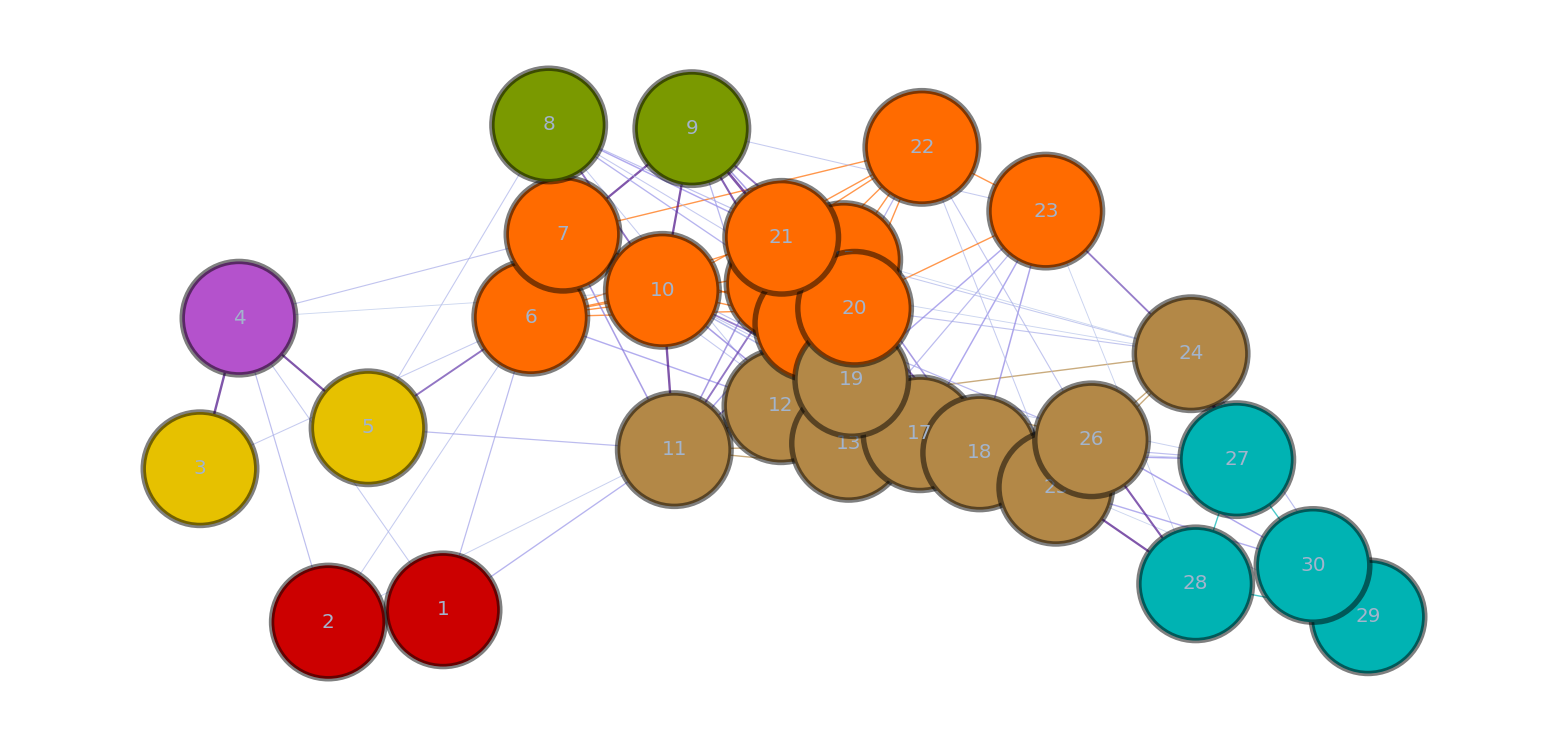

```mathematica
style2 = Switch[# ,
"A",EdgeForm[Directive[Thickness[.0025], Opacity[.5],Lighter[Black, 0]]],  
"B",EdgeForm[Directive[Thickness[.0025],Opacity[.5], Lighter[Black,0]]],
"C",EdgeForm[Directive[Thickness[.0025],Opacity[.5], Lighter[Black,0]]],
"D",EdgeForm[Directive[Thickness[.0025],Opacity[.5], Lighter[Black,0]]]
] & /@ id;
stylesList2 = Style[#[[2]] , #[[1]]] & /@ ({style2, ids} // Transpose);
HighlightGraph[highlighted,stylesList2,ImageSize->2000]
```

```mathematica
clustersStrings
```

{{1,2},{3,5},{4},{6,7,10,14,15,16,20,21,22,23},{8,9},{11,12,13,17,18,19,24,25,26},{27,28,29,30}}

```mathematica
edges=Table[EdgeForm[Directive[Thickness[.002],Opacity[.75],colors[[i]]]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
HighlightGraph[graph2, Style[#[[2]] ,#[[1]],#[[3]]] & /@ ({edges,ToString/@ids,style} // Transpose)];
```